```mathematica
ClearAll[Ausgleichsgerade];
Ausgleichsgerade[xValues_,yValues_]:=(
If[Length[xValues]==Length[xValues],,Throw["Arrays sind nicht gleich lang"]
];
ClearAll[n,xxValues,xyValues,Δ,xSum,ySum,xxSum,xySum,a,b,s2,σa,σb,Δc,r,yTrue,σy];

n=Length[xValues];

xxValues=Table[xValues[[i]]^2,{i,1,n}];
xyValues=Table[xValues[[i]]*yValues[[i]],{i,1,n}];

xSum=Sum[xValues[[i]],{i,1,n}];
ySum=Sum[yValues[[i]],{i,1,n}];
xxSum=Sum[xxValues[[i]],{i,1,n}];
xySum=Sum[xyValues[[i]],{i,1,n}];

Δ=n*xxSum-xSum^2;
a=1/Δ*(xxSum*ySum-xSum*xySum);
b=1/Δ*(n*xySum-xSum*ySum);

r=(n*xySum-xSum*ySum)/(√((n*xxSum-xSum^2)*(n*Sum[yValues[[i]]^2,{i,1,n}]-ySum^2)));

s2=1/(n-2)*Sum[(yValues[[i]]-a-b*xValues[[i]])^2,{i,1,n}];
σa=√(s2/Δ*xxSum);
σb=√(n*s2/Δ);

x=xSum/n;
y=ySum/n;
Δc=√(x^2*σb^2+σa^2);

yTrue=Table[b*xValues[[i]]+a,{i,1,n}];
σy=Table[(yValues[[i]]-yTrue[[i]])^2,{i,1,n}];
yTrueSum:=Sum[yTrue[[i]],{i,1,n}];
σySum:=Sum[σy[[i]],{i,1,n}];

Print["\n",TableForm[{Join[xValues,{"",xSum}],Join[yValues,{"",ySum}],Join[yTrue,{"",yTrueSum}],Join[σy,{"",σySum}],Join[xxValues,{"",xxSum}],Join[xyValues,{"",xySum}]},TableDirections->Row,TableSpacing->{3, 1},TableHeadings->{{"x_i", "y_i","y","(y-y_i)^2","x_i^2","x_i*y_i" },Join[Table["",{i,1,n+1}],{"Sum:"}]}]];
Print["\n","a = ",a," ± ",σa,"\n","b = ",b," ± ",σb,"\n","r = ",r,"\n","x̄ = ",x,"; ȳ = ",y,"; Δc = ",Δc];
Print["\n","=> y = (b ± Δb)*(x - x̄) + (ȳ ± Δc)","\n","=> y = (",b," ± ",σb,")*(x - ",x,") + ",y," ± ",Δc];
Show[{
ListPlot[Table[{xValues[[i]],yValues[[i]]},{i,1,n}],PlotStyle->Red,PlotMarkers->"X"],
Plot[{
(b)*(xCoord-x)+y,
(b+σb)*(xCoord-x)+y+Δc,
(b-σb)*(xCoord-x)+y+Δc,
(b+σb)*(xCoord-x)+y-Δc,
(b-σb)*(xCoord-x)+y-Δc
},
{xCoord,0,9},
PlotStyle->{Automatic,RGBColor[169/256,195/256,97/256,0.7],RGBColor[169/256,195/256,97/256,0.7],RGBColor[230/256,171/256,68/256,0.7],RGBColor[230/256,171/256,68/256,0.7]}
]
},ImageSize->Full]
)
```

| x_i | y_i | y | (y-y_i)^2 | x_i^2 | x_i*y_i
 | 0.23 | -73.5 | -73.1746 | 0.105915 | 0.0529 | -16.905
 | 0.96 | -71. | -71.6344 | 0.402526 | 0.9216 | -68.16
 | 2.18 | -68.9 | -69.0606 | 0.0257849 | 4.7524 | -150.202
 | 3.03 | -66.7 | -67.2673 | 0.321835 | 9.1809 | -202.101
 | 3.84 | -65.8 | -65.5584 | 0.0583599 | 14.7456 | -252.672
 | 4.98 | -64.1 | -63.1533 | 0.896188 | 24.8004 | -319.218
 | 6.1 | -61.5 | -60.7904 | 0.503492 | 37.21 | -375.15
 | 7.19 | -58.7 | -58.4908 | 0.0437559 | 51.6961 | -422.053
 | 8.29 | -55.1 | -56.1701 | 1.14515 | 68.7241 | -456.779
 |  |  |  |  |  | 
Sum: | 36.8 | -585.3 | -585.3 | 3.503 | 212.084 | -2263.24

a = -73.6598 ± 0.43749
b = 2.10973 ± 0.090123
r = 0.993674
x̄ = 4.08889; ȳ = -65.0333; Δc = 0.572007

=> y = (b ± Δb)*(x - x̄) + (ȳ ± Δc)
=> y = (2.10973 ± 0.090123)*(x - 4.08889) + -65.0333 ± 0.572007

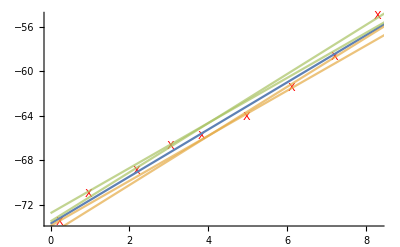

```mathematica
(*xValues={0.20,1.17,1.96,2.98,4.05,5.12,5.93,7.01,8.24};
yValues={52.4,54.6,57.7,59.5,62.7,65.6,67.0,69.0,72.8};*)

xValues={0.23,0.96,2.18,3.03,3.84,4.98,6.10,7.19,8.29};
yValues={-73.5,-71.0,-68.9,-66.7,-65.8,-64.1,-61.5,-58.7,-55.1};

Ausgleichsgerade[xValues,yValues]
```